# diffusion constants

```mathematica
p0s={3.85,3.825,3.80,3.75};
```

```mathematica
temperatures={{0.039 ,0.016, 0.01 ,0.005 ,0.00385, 0.0025 ,0.002, 0.001 ,0.0005 ,0.00033 ,0.00025, 0.00014, 0.000091,0.000077,0.000054, 0.000045, 0.000036},{0.063 ,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015, 0.001, 0.00067 ,0.0005},{0.063 ,0.039 ,0.03105, 0.025, 0.016 ,0.01 ,0.008 ,0.0063, 0.005, 0.00385, 0.0031, 0.0028 ,0.0025 ,0.0022},{0.063, 0.039, 0.03105, 0.025 ,0.02, 0.016, 0.014,0.012 ,0.011, 0.01, 0.0093}};
 records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};(*id for configurations*)
```

```mathematica
(*The dimentionas are {p0,T,id}*)
rawDiffusionConstants={{{0.04208038690045594,0.05575256447484832,0.0410715338614643,0.04395294881771476,0.04463286126062931,0.04116756292163692,0.0450023612342618,0.04229695560058631,0.044363534484604075,0.04419347599121143},{0.013536158129007351,0.015634893304914455,0.01392472067913504,0.015058360561325297,0.014212267454397121,0.012718698432196756,0.017049770376106197,0.013584860780321393,0.014193340637412726,0.013614980299416482},{0.008150281753572176,0.008243503984628378,0.007619233853513725,0.008144095153512642,0.008654734523475474,0.008024357715234407,0.009201805063992891,0.008392520756945984,0.009065503524070564,0.007674145250367947},{0.003645018786004525,0.004024389366551731,0.003220332381171624,0.0036448063775274104,0.004507134359564465,0.0039058557980560086,0.003809295080476251,0.0036368462180397347,0.0037031649361890877,0.0035950754600132346},{0.0024338458141006402,0.0032605556613370013,0.0033046463616578656,0.002238071758244277,0.002879521469027557,0.0030501830302471396,0.002990487366391799,0.002347902389724112,0.0024493788968106855,0.0036887030520166533},{0.001895749483888484,0.0020414707514198266,0.0013711118564617303,0.001934115806158817,0.0015112909564514107,0.0014439792732723244,0.0018433411162664729,0.001591765725466581,0.0016656333428007437,0.0014652526915525828},{0.0012089607429194358,0.0011758247790479306,0.0013503630476392654,0.0010675065980726298,0.0009346965894038761,0.0011451919310235142,0.0010617059084860546,0.0010704333732809521,0.0012980057655754937,0.0009500246703253365},{0.000496305268252824,0.00042428005556554806,0.0006538172848228773,0.00038982840655910896,0.0004449273332982586,0.00043676597065453633,0.0005539641077285147,0.000494872156208392,0.00046115841858355473,0.00044605882849739774},{0.00023443211711133232,0.00015507984444851027,0.00014668479354211866,0.00015713789700863318,0.00017668730066056835,0.00015868323504833834,0.00015759857668415868,0.00015039783884208393,0.0001638806240994259,0.00019164640733477096},{0.00009944772782308228,0.00009028571477342927,0.00007626563665315052,0.00009277563395835542,0.00008644710782597441,0.00006692381850485903,0.000086093350455502,0.00010320312827110585,0.00008630295928404871,0.00009468642640129486},{0.000056814827270863624,0.000044376316872376737,0.00005178198743789438,0.00005290455368374127,0.000047278833414259687,0.00007701717958525611,0.000055064710673185976,0.0000486463155758523,0.000048265710240660914,0.0000486499930330659},{0.00002110422561138355,0.00002168710161518569,0.000018364920254764626,0.000021444249886224716,0.00002418891718906141,0.000020460487717645157,0.000021134814502324434,0.00001967094053318297,0.000020154134851906802,0.00002116695423232572},{8.470245092635098*^-6,8.139203393619243*^-6,0.000012883862156238315,8.633148274855083*^-6,8.428791436495183*^-6,0.000010177657783391242,9.798782895491664*^-6,7.501396685645301*^-6,8.470107776527402*^-6,8.896101965159271*^-6},{6.4958124132682525*^-6,7.898820800118783*^-6,6.1779037594601595*^-6,6.403898819109405*^-6,6.054594271116307*^-6,8.004471229273264*^-6,6.0476667081877725*^-6,7.705684504537273*^-6,6.75083615132787*^-6,6.649089877555755*^-6},{3.7509662922566458*^-6,4.119797024196644*^-6,3.991817579690363*^-6,6.835238172016235*^-6,4.610298278957706*^-6,3.5827699542012147*^-6,3.393778718358561*^-6,3.971670958973348*^-6,3.4926877420064474*^-6,3.468119900251464*^-6},{2.5339305194379536*^-6,2.282813785295997*^-6,2.692289565020555*^-6,3.7111456694283042*^-6,2.037691721358761*^-6,2.493794943081022*^-6,2.7947799654008477*^-6,3.013543213683208*^-6,2.644149529504664*^-6,2.3191214852500266*^-6},{2.1051844743692026*^-6,1.8973131363688753*^-6,1.787194918616841*^-6,1.977679691152661*^-6,1.5371642911903493*^-6,1.8436983929983648*^-6,1.7505430984564134*^-6,1.9825611969866656*^-6,2.083783500432821*^-6,1.8282964719696161*^-6}},{{0.06791202197292838,0.07170146056911034,0.06546192518080712,0.06532890394153154,0.06402402064821815,0.06735801958915609,0.0677893365386487,0.06805046668970198,0.06386454980420984,0.0670479435894507},{0.03839867403505891,0.035747088068632256,0.03454502073559868,0.03581673864171575,0.039368995523461424,0.03498227634298344,0.04005428628318374,0.03684067590263201,0.0369609816011426,0.03568218460802702},{0.023120689793092435,0.02547371790237288,0.024916701784060056,0.028067702998553663,0.02786810972887557,0.026385101509271366,0.024329565507473203,0.024054633723510896,0.02542121786389608,0.024665276490496414},{0.010660365212887716,0.011084010147805586,0.010696225990854251,0.010087668083943032,0.009581857889998534,0.010218903190133225,0.011919956442384276,0.009646851419270986,0.010216477205476677,0.009765486969891449},{0.005486398192451692,0.004820102977930058,0.0054215889358816965,0.005322996760229767,0.005766962529777565,0.005027371868381872,0.004789233579500216,0.004432522301336392,0.005136740646770659,0.006408076446189666},{0.0035887941546529,0.004194192782820844,0.0038345507171514233,0.0049049585441167986,0.0035198130783747976,0.003951840864741585,0.003089889542478667,0.003753747342394362,0.003491826455199825,0.0031953405715114515},{0.002471274699356175,0.002657624701703597,0.00259879511845823,0.0023812391165310472,0.002696831302264033,0.0027561151315228785,0.002518541478072477,0.002385942073164285,0.0025596692252470702,0.0027941661397065244},{0.0018878920068842197,0.0015875285899021503,0.0021263952937287255,0.0021339403742218314,0.0018041024329489928,0.0017555377548152764,0.0023241060563618356,0.002050444638854757,0.0016001991764523788,0.0018200369577666105},{0.0012842793160680618,0.0012242228875375704,0.0011326352529561652,0.0011504568005990547,0.0012341978849982884,0.0015076706674117908,0.001292274027664069,0.0013315464388328451,0.0014588622432471054,0.0013075609863943437},{0.0009308046803538823,0.0010190588478606061,0.000848695618645144,0.0009481317286362841,0.0010203367579825107,0.0009041232020655842,0.0009610898298595236,0.0008376797103895503,0.0013529031017046266,0.0010459689942697757},{0.0006740708696895834,0.0006470708227286285,0.000573780051137171,0.0005445181080309061,0.0007993718890201823,0.0005152773559522434,0.0007366400108698554,0.0006845568313512444,0.0005486463825181228,0.0006257817622806682},{0.0005672672210930595,0.0004411637112767503,0.00044447771211012156,0.0005078198574721191,0.00036729385770685745,0.0004461850402063165,0.00040423488588184326,0.0004515249531251708,0.00045736687065918875,0.000478337034044021},{0.00032562183181158896,0.0002276198168919827,0.00025965924764958744,0.0002955546248859893,0.0002816266600961656,0.00027424986415675343,0.0002255670855353627,0.00025760499851157695,0.0002412475203894627,0.00023413962334879805},{0.00010853514869878216,0.00009540724201025761,0.00009985801405243157,0.00008979896743318267,0.00008907317746041911,0.0001343503727066285,0.0000929151383267091,0.00010369307429624277,0.00011240397344551301,0.00009568775255965472},{0.000033096378621229376,0.00003719910490989621,0.000029180281479000242,0.00002564319158807176,0.00003985450893875104,0.000026629364774200122,0.00003080987009145615,0.00003160354885960629,0.0000349225797652031,0.0000299217103783428},{0.00001381940738885942,0.000012921797814408297,0.000012376687765319037,0.000014169596399511224,0.000011630120904283681,0.000015424953253295716,0.000013539042593221476,0.000011597226924653814,0.000011387615740701891,0.000013562333506273697}},{{0.05887979526582862,0.059234085559979825,0.06037337509350302,0.05604110883730617,0.05379406036919042,0.06097936797663025,0.056751184397896295,0.06254452527325735,0.056443686938088905,0.06184442863448481},{0.031057909966820806,0.03345484587884472,0.030812038374661167,0.02892822409714404,0.03273314527169745,0.031383071914977245,0.027612293636032195,0.02748781543181674,0.02633474146208383,0.029142925865766157},{0.022523459492160117,0.021252021163347252,0.019133942058104373,0.019439016289198797,0.02222567254333415,0.018174822201956223,0.01836110153676936,0.01989515873323027,0.019851278725064134,0.02001861388126738},{0.013222388258221482,0.014160281222876898,0.014081124554928345,0.012992920095120035,0.014424010797581306,0.014443656866546882,0.015090822901824019,0.01397438898890677,0.01485495420199365,0.01312852143075802},{0.006359034149491122,0.006277656953989769,0.006520186169367528,0.00713156163271127,0.006456636458411897,0.006717368262417281,0.006706973163882261,0.006031311312936073,0.006737245412976199,0.006480058944225784},{0.0033705703973221078,0.0035443441156005266,0.0031117349705390407,0.002703611909387333,0.002811402876791629,0.0025437385488322724,0.0028106263705604683,0.002841051245346853,0.002532882792809483,0.0027198169240765977},{0.0018447323760778654,0.0018554877809078022,0.001694301164222122,0.0019987212128608463,0.0015950552896601355,0.002169443264867503,0.0018850653751093546,0.001532020626895797,0.0016672285286883108,0.0018879831194415651},{0.0009210606020263739,0.0012227510688287342,0.0010102246681235136,0.0010968366770890616,0.001257911877513048,0.0009869883832320553,0.0009707768170093815,0.0011573820648944585,0.0010750373648494313,0.001091539478617886},{0.0006539746886617127,0.0007137680567067648,0.0007784392958085894,0.0005945484461158354,0.000637191995641527,0.0007264556435684756,0.0006055467247456015,0.0007006078673883414,0.0006210255249516729,0.0008967683110157569},{0.000334274516619345,0.0003185343848642534,0.00029542550494330834,0.00025266091263295736,0.0003979571430088256,0.0002664811292234168,0.0004528850982629467,0.00035362034416748755,0.00030818065804160566,0.0002753787938322095},{0.0001469897650102306,0.00011501609986344583,0.00013157883900318022,0.00015494645859364674,0.00014237847125173525,0.00015192039732069614,0.000132354312468471,0.00013179916536574184,0.00012841044073732316,0.00010776955435372069},{0.00007018796377981348,0.00009434300784174333,0.00008085358950362444,0.00009124181933657058,0.00007888709969025657,0.00009558277437212998,0.00010542823900251458,0.00008437239325434234,0.00009183200106710314,0.00009262716360742945},{0.00006126564556190351,0.00005003963019602621,0.000059068241809211114,0.00004980789693950827,0.0000504818459277799,0.000047513743282640125,0.000046338557161541265,0.00005964592642913469,0.0000494667022362847,0.000047600821769659704},{0.000027576251275919866,0.000029600436465425886,0.000022880711694534578,0.00003061906929112119,0.000031202211877573724,0.00003228113182344704,0.00002639041587922469,0.000030297798848169395,0.00002778087641546495,0.000029190162873175264}},{{0.04244624687573254,0.03942497873614467,0.04178526124527304,0.041890288178217765,0.03925221143074747,0.042351006157501016,0.042228433829578145,0.04199726467417135,0.04326402442936322,0.041731684170986195},{0.016710223674849773,0.01615862105604736,0.01909242737987126,0.016515855670050157,0.019372943597436038,0.016858808343217915,0.018543081441716968,0.015941325535913098,0.01793125393058784,0.017523251969176194},{0.012167024493331886,0.010318596131144239,0.012039345349498272,0.013492067321657676,0.011722248305844174,0.012187757667443486,0.011732446872843447,0.010245161232941277,0.01118592922433291,0.010308845207510874},{0.006617838164846879,0.006896021756732782,0.007082983309879642,0.007594831267494215,0.0064900421283861885,0.007982218250809447,0.00663184212775356,0.006417627453083028,0.006532671818507896,0.006925918010097402},{0.003731708018788871,0.003819791376363536,0.003751194056841099,0.004671113306590611,0.004328355377956947,0.003991929451964503,0.004381990073199389,0.004070336656702939,0.003241079231228718,0.003668368444267585},{0.001982910831877599,0.0017691109869684828,0.0020145194958339336,0.002078041365332533,0.001588151722079129,0.0016540999409768388,0.001862931521554689,0.0015789414649063386,0.002056287340636384,0.002048651157866037},{0.001153472378360955,0.0010265025798958309,0.0010182714516633487,0.0011584618766634553,0.001047946024569356,0.001066733570448964,0.0010618564247679462,0.0011450929067218188,0.0009285643395822691,0.0010803081642521118},{0.0003552707427896745,0.000428607654683319,0.00037356312490394156,0.0003358732141105303,0.0003758732028923843,0.00043900523561151285,0.0004308835739767879,0.0004103708027528057,0.0003650136442820576,0.00035489338909485096},{0.00018138570743152547,0.00018298231407507263,0.00018013180240707222,0.00023682453116881266,0.00016621944259600426,0.00017272895947072548,0.00017669889963562534,0.00014307784102978428,0.0001390719159237892,0.0001569933409138861},{0.000057193709905118996,0.00004437818127567935,0.00006378805351994754,0.00006142276626923708,0.00006723962789188855,0.00005593997254315376,0.00007401581033538658,0.00005021897569254396,0.00006336529588918281,0.000053252160758203696},{0.000024459330084410164,0.000023662438390344698,0.000025149205532350812,0.0000225000599386129,0.000021994283108590597,0.00001962500854057149,0.00002107634518303264,0.00003097235790885112,0.000026622335288679806,0.00002218473842952732}}};
```

```mathematica
(*Mean and std*)
```

```mathematica
finalD={{0.0440.004,0.01440.0013,0.00830.0005,0.003770.00034,0.00290.0005,0.001680.00024,0.001130.00014,0.000480.00008,0.0001690.000026,0.0000880.000011,0.0000539,0.000020915,9.11.510^-6,6.80.810^-6,4.11.010^-6,2.70.510^-6,1.880.1710^-6},{0.06690.0023,0.03680.0019,0.02540.0016,0.01040.0007,0.00530.0006,0.00380.0005,0.002580.00015,0.001910.00024,0.001290.00012,0.000990.00015,0.000630.00009,0.000460.00005,0.0002620.000032,0.0001020.000014,0.0000324,0.000013013},{0.05870.0028,0.02990.0024,0.02010.0015,0.01400.0007,0.006540.00030,0.002900.00034,0.001810.00019,0.001080.00011,0.000690.00009,0.000330.00006,0.0001340.000015,0.0000890.000010,0.0000526,0.000028827},{0.04160.0013,0.01750.0012,0.01150.0010,0.00690.0005,0.00400.0004,0.001860.00020,0.001070.00007,0.000390.00004,0.0001740.000027,0.0000599,0.000023832}};
```

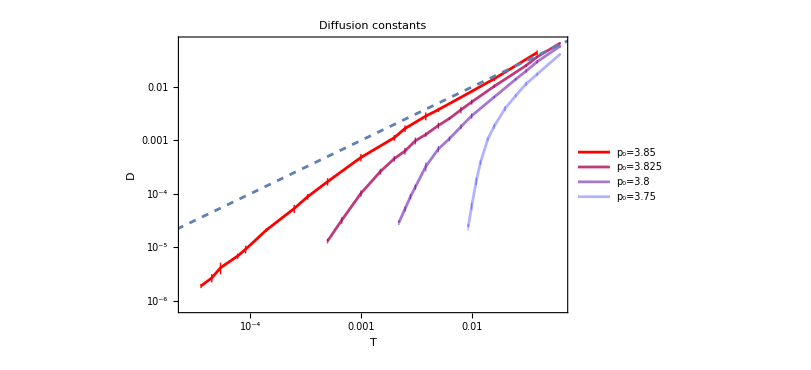

```mathematica
Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],finalD[[p,T]]},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}],Joined->True,PlotStyle->redBluePlotConfig[Length[p0s]],FrameLabel->{"T","D"},ImageSize->600,PlotLabel->"Diffusion constants",PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}]],LogLogPlot[x,{x,0.00001,0.1},PlotStyle->Dashed]]
```